2 - 7 General solution
Find a general solution.

3.  y_1'=y_2+ⅇ^(3t)
y_2'=y_1-3 ⅇ^(3t)

```mathematica
ClearAll["Global`*"]
```

As in the last section, there will be rearranging, recasting, and substitutions after the solution appears in order to make its form like the text answer.

```mathematica
e1={y1'[t]==y2[t]+ⅇ^(3 t),y2'[t]==y1[t]-3 ⅇ^(3 t)}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==ⅇ^(3 t)+y2[t],y2'[t]==-3 ⅇ^(3 t)+y1[t]}

{{y1→Function[{t},1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2]],y2→Function[{t},1/4 ⅇ^t (-1+ⅇ^(2 t))^2-1/4 ⅇ^t (1+ⅇ^(2 t))^2+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]]}}

```mathematica
e3=e2[[1,1,2,2]]
```

1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2]

```mathematica
e4=Expand[e3]
```

1/2 ⅇ^-t C[1]+1/2 ⅇ^t C[1]-1/2 ⅇ^-t C[2]+1/2 ⅇ^t C[2]

```mathematica
e5=Collect[e4,ⅇ^-t]
```

ⅇ^-t (C[1]/2-C[2]/2)+ⅇ^t (C[1]/2+C[2]/2)

```mathematica
e6=e5/.{(C[1]/2-C[2]/2)->c1,(C[1]/2+C[2]/2)->c2}
```

c1 ⅇ^-t+c2 ⅇ^t

```mathematica
e7=e2[[1,2,2,2]]
```

1/4 ⅇ^t (-1+ⅇ^(2 t))^2-1/4 ⅇ^t (1+ⅇ^(2 t))^2+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]

```mathematica
e8=Expand[e7]
```

-ⅇ^(3 t)-1/2 ⅇ^-t C[1]+1/2 ⅇ^t C[1]+1/2 ⅇ^-t C[2]+1/2 ⅇ^t C[2]

```mathematica
e9=Collect[e8,ⅇ^t]
```

-ⅇ^(3 t)+ⅇ^-t (-C[1]/2+C[2]/2)+ⅇ^t (C[1]/2+C[2]/2)

```mathematica
e10=e9/.{(-C[1]/2+C[2]/2)->-c1,(C[1]/2+C[2]/2)->c2}
```

-c1 ⅇ^-t+c2 ⅇ^t-ⅇ^(3 t)

1. Above: The expressions in the green cells match the text answers for y_1 and y_2 respectively. The substitutions of symbolic constants shown in the yellow cells match values of constants between the two function expressions, demonstrating that the constant substitution system is self-consistent and consistent with the text.

5.  y_1'=4 y_1+y_2+0.6t
y_2'=2 y_1+3 y_2-2.5t

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==4 y1[t]+y2[t]+0.6 t,y2'[t]==2 y1[t]+3 y2[t]-2.5 t}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==0.6 t+4 y1[t]+y2[t],y2'[t]==-2.5 t+2 y1[t]+3 y2[t]}

{{y1→Function[{t},-0.333333 (1. ⅇ^(2. t)-1. ⅇ^(5. t)) (-2.06667 ⅇ^(-2. t) (-0.25-0.5 t)-0.433333 ⅇ^(-5. t) (-0.04-0.2 t))+0.333333 (1. ⅇ^(2. t)+2. ⅇ^(5. t)) (1.03333 ⅇ^(-2. t) (-0.25-0.5 t)-0.433333 ⅇ^(-5. t) (-0.04-0.2 t))+0.333333 (1. ⅇ^(2. t)+2. ⅇ^(5. t)) C[1]-0.333333 (1. ⅇ^(2. t)-1. ⅇ^(5. t)) C[2]],y2→Function[{t},0.666667 (1. ⅇ^(2. t)+0.5 ⅇ^(5. t)) (-2.06667 ⅇ^(-2. t) (-0.25-0.5 t)-0.433333 ⅇ^(-5. t) (-0.04-0.2 t))-0.666667 (1. ⅇ^(2. t)-1. ⅇ^(5. t)) (1.03333 ⅇ^(-2. t) (-0.25-0.5 t)-0.433333 ⅇ^(-5. t) (-0.04-0.2 t))-0.666667 (1. ⅇ^(2. t)-1. ⅇ^(5. t)) C[1]+0.666667 (1. ⅇ^(2. t)+0.5 ⅇ^(5. t)) C[2]]}}

```mathematica
e3=e2[[1,1,2,2]]
```

-0.333333 (1. ⅇ^(2. t)-1. ⅇ^(5. t)) (-2.06667 ⅇ^(-2. t) (-0.25-0.5 t)-0.433333 ⅇ^(-5. t) (-0.04-0.2 t))+0.333333 (1. ⅇ^(2. t)+2. ⅇ^(5. t)) (1.03333 ⅇ^(-2. t) (-0.25-0.5 t)-0.433333 ⅇ^(-5. t) (-0.04-0.2 t))+0.333333 (1. ⅇ^(2. t)+2. ⅇ^(5. t)) C[1]-0.333333 (1. ⅇ^(2. t)-1. ⅇ^(5. t)) C[2]

```mathematica
e4=Simplify[e3]
```

ⅇ^(-3. t) (-8.67362×10^-19+ⅇ^(3. t) (-0.241-0.43 t)+ⅇ^(6. t) (-2.77556×10^-17-5.55112×10^-17 t)+ⅇ^(5. t) (0.333333 C[1]-0.333333 C[2])+ⅇ^(8. t) (0.666667 C[1]+0.333333 C[2]))

```mathematica
e5=Expand[e4]
```

-0.241-8.67362×10^-19 ⅇ^(-3. t)-2.77556×10^-17 ⅇ^(3. t)-0.43 t-5.55112×10^-17 ⅇ^(3. t) t+0.333333 ⅇ^(2. t) C[1]+0.666667 ⅇ^(5. t) C[1]-0.333333 ⅇ^(2. t) C[2]+0.333333 ⅇ^(5. t) C[2]

```mathematica
e6=Chop[e5,10^-16]
```

-0.241-0.43 t+0.333333 ⅇ^(2. t) C[1]+0.666667 ⅇ^(5. t) C[1]-0.333333 ⅇ^(2. t) C[2]+0.333333 ⅇ^(5. t) C[2]

```mathematica
e7=Collect[e6,{ⅇ^(2. t),ⅇ^(5. t)}]
```

-0.241-0.43 t+ⅇ^(2. t) (0.333333 C[1]-0.333333 C[2])+ⅇ^(5. t) (0.666667 C[1]+0.333333 C[2])

```mathematica
e8=e7/.{(0.3333333333333334 C[1]-0.3333333333333333 C[2])->c2,(0.6666666666666666 C[1]+0.3333333333333333 C[2])->c1}
```

-0.241+c2 ⅇ^(2. t)+c1 ⅇ^(5. t)-0.43 t

```mathematica
e9=e2[[1,2,2,2]]
```

0.666667 (1. ⅇ^(2. t)+0.5 ⅇ^(5. t)) (-2.06667 ⅇ^(-2. t) (-0.25-0.5 t)-0.433333 ⅇ^(-5. t) (-0.04-0.2 t))-0.666667 (1. ⅇ^(2. t)-1. ⅇ^(5. t)) (1.03333 ⅇ^(-2. t) (-0.25-0.5 t)-0.433333 ⅇ^(-5. t) (-0.04-0.2 t))-0.666667 (1. ⅇ^(2. t)-1. ⅇ^(5. t)) C[1]+0.666667 (1. ⅇ^(2. t)+0.5 ⅇ^(5. t)) C[2]

```mathematica
e10=Simplify[e9]
```

0.534+1.73472×10^-18 ⅇ^(-3. t)+1.12 t+ⅇ^(5. t) (0.666667 C[1]+0.333333 C[2])+ⅇ^(2. t) (-0.666667 C[1]+0.666667 C[2])

```mathematica
e11=Chop[e10,10^-16]
```

0.534+1.12 t+ⅇ^(5. t) (0.666667 C[1]+0.333333 C[2])+ⅇ^(2. t) (-0.666667 C[1]+0.666667 C[2])

```mathematica
e12=e11/.{(0.6666666666666669 C[1]+0.3333333333333334 C[2])->c1,(-0.6666666666666669 C[1]+0.6666666666666667 C[2])->-2 c2}
```

0.534-2 c2 ⅇ^(2. t)+c1 ⅇ^(5. t)+1.12 t

1. Above: The expressions in the green cells match the text answers for y_1 and y_2 respectively. The substitutions of symbolic constants shown in the yellow cells match values of constants between the two function expressions, demonstrating that the constant substitution system is self-consistent and consistent with the text.

7.  y_1'=-3 y_1-4 y_2+11t+15
y_2'=5 y_1+6 y_2+3 ⅇ^-t-15t-20

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==-3 y1[t]-4 y2[t]+11 t+15,y2'[t]==5 y1[t]+6 y2[t]+3 ⅇ^-t-15 t-20}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==15+11 t-3 y1[t]-4 y2[t],y2'[t]==-20+3 ⅇ^-t-15 t+5 y1[t]+6 y2[t]}

{{y1→Function[{t},-ⅇ^t (-5+4 ⅇ^t) (4 ⅇ^(-3 t)+ⅇ^(-2 t) (-20-8 t)+ⅇ^-t (10+5 t))-4 ⅇ^t (-1+ⅇ^t) (-5 ⅇ^(-3 t)+ⅇ^-t (-10-5 t)+ⅇ^(-2 t) (47/2+10 t))-ⅇ^t (-5+4 ⅇ^t) C[1]-4 ⅇ^t (-1+ⅇ^t) C[2]],y2→Function[{t},5 ⅇ^t (-1+ⅇ^t) (4 ⅇ^(-3 t)+ⅇ^(-2 t) (-20-8 t)+ⅇ^-t (10+5 t))+ⅇ^t (-4+5 ⅇ^t) (-5 ⅇ^(-3 t)+ⅇ^-t (-10-5 t)+ⅇ^(-2 t) (47/2+10 t))+5 ⅇ^t (-1+ⅇ^t) C[1]+ⅇ^t (-4+5 ⅇ^t) C[2]]}}

```mathematica
e3=e2[[1,1,2,2]]
```

-ⅇ^t (-5+4 ⅇ^t) (4 ⅇ^(-3 t)+ⅇ^(-2 t) (-20-8 t)+ⅇ^-t (10+5 t))-4 ⅇ^t (-1+ⅇ^t) (-5 ⅇ^(-3 t)+ⅇ^-t (-10-5 t)+ⅇ^(-2 t) (47/2+10 t))-ⅇ^t (-5+4 ⅇ^t) C[1]-4 ⅇ^t (-1+ⅇ^t) C[2]

```mathematica
e4=Simplify[e3]
```

ⅇ^-t (-2-ⅇ^t (4+3 t)-4 ⅇ^(3 t) (C[1]+C[2])+ⅇ^(2 t) (5 C[1]+4 C[2]))

```mathematica
e5=Expand[e4]
```

-4-2 ⅇ^-t-3 t+5 ⅇ^t C[1]-4 ⅇ^(2 t) C[1]+4 ⅇ^t C[2]-4 ⅇ^(2 t) C[2]

```mathematica
e6=Collect[e5,{ⅇ^(2 t),ⅇ^t}]
```

-4-2 ⅇ^-t-3 t+ⅇ^(2 t) (-4 C[1]-4 C[2])+ⅇ^t (5 C[1]+4 C[2])

```mathematica
e7=e6/.{(-4 C[1]-4 C[2])->4 c2,(5 C[1]+4 C[2])->c1}
```

-4-2 ⅇ^-t+c1 ⅇ^t+4 c2 ⅇ^(2 t)-3 t

```mathematica
e8=e2[[1,2,2,2]]
```

5 ⅇ^t (-1+ⅇ^t) (4 ⅇ^(-3 t)+ⅇ^(-2 t) (-20-8 t)+ⅇ^-t (10+5 t))+ⅇ^t (-4+5 ⅇ^t) (-5 ⅇ^(-3 t)+ⅇ^-t (-10-5 t)+ⅇ^(-2 t) (47/2+10 t))+5 ⅇ^t (-1+ⅇ^t) C[1]+ⅇ^t (-4+5 ⅇ^t) C[2]

```mathematica
e9=Simplify[e8]
```

15/2+ⅇ^-t+5 t+5 ⅇ^(2 t) (C[1]+C[2])-ⅇ^t (5 C[1]+4 C[2])

```mathematica
e10=e9/.{(C[1]+C[2])->-c2,(5 C[1]+4 C[2])->c1}
```

15/2+ⅇ^-t-c1 ⅇ^t-5 c2 ⅇ^(2 t)+5 t

1. Above: The expressions in the green cells match the text answers for y_1 and y_2 respectively. The substitutions of symbolic constants shown in the yellow cells match values of constants between the two function expressions, demonstrating that the constant substitution system is self-consistent and consistent with the text.

10 - 15 Initial value problem
Solve, showing details.

11.  y_1'=y_2+6 ⅇ^(2t)
y_2'=y_1-ⅇ^(2t)
y_1[0]=1, y_2[0]=0

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==y2[t]+6 ⅇ^(2 t),y2'[t]==y1[t]-ⅇ^(2 t),y1[0]==1,y2[0]==0}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==6 ⅇ^(2 t)+y2[t],y2'[t]==-ⅇ^(2 t)+y1[t],y1[0]==1,y2[0]==0}

{{y1→Function[{t},1/3 ⅇ^-t (-2-6 ⅇ^(2 t)+11 ⅇ^(3 t))],y2→Function[{t},2/3 ⅇ^-t (-1+ⅇ^t)^2 (1+2 ⅇ^t)]}}

```mathematica
e3=e2[[1,1,2,2]]
```

1/3 ⅇ^-t (-2-6 ⅇ^(2 t)+11 ⅇ^(3 t))

```mathematica
e4=Expand[e3]
```

-(2 ⅇ^-t)/3-2 ⅇ^t+(11 ⅇ^(2 t))/3

```mathematica
e5=e4/.(-(2 ⅇ^-t)/3-2 ⅇ^t)->ExpToTrig[-(2 ⅇ^-t)/3-2 ⅇ^t]
```

(11 ⅇ^(2 t))/3-(8 Cosh[t])/3-(4 Sinh[t])/3

```mathematica
e6=e2[[1,2,2,2]]
```

2/3 ⅇ^-t (-1+ⅇ^t)^2 (1+2 ⅇ^t)

```mathematica
e7=Expand[e6]
```

(2 ⅇ^-t)/3-2 ⅇ^t+(4 ⅇ^(2 t))/3

```mathematica
e8=e7/.((2 ⅇ^-t)/3-2 ⅇ^t)->ExpToTrig[(2 ⅇ^-t)/3-2 ⅇ^t]
```

(4 ⅇ^(2 t))/3-(4 Cosh[t])/3-(8 Sinh[t])/3

1. Above: The top and bottom green cell expressions match the text answers for y_1 and y_2 respectively.

13.  y_1'=y_2-5Sin[t]
y_2'=-4 y_1+17Cos[t]
y_1[0]=5, y_2[0]=2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==y2[t]-5 Sin[t],y2'[t]==-4 y1[t]+17 Cos[t],y1[0]==5,y2[0]==2}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==-5 Sin[t]+y2[t],y2'[t]==17 Cos[t]-4 y1[t],y1[0]==5,y2[0]==2}

{{y1→Function[{t},1/4 (4 Cos[2 t]+7 Cos[t] Cos[2 t]+9 Cos[2 t] Cos[3 t]+4 Sin[2 t]+7 Sin[t] Sin[2 t]+9 Sin[2 t] Sin[3 t])],y2→Function[{t},1/2 (4 Cos[2 t]+7 Cos[2 t] Sin[t]-4 Sin[2 t]-7 Cos[t] Sin[2 t]-9 Cos[3 t] Sin[2 t]+9 Cos[2 t] Sin[3 t])]}}

```mathematica
e3=e2[[1,1,2,2]]
```

1/4 (4 Cos[2 t]+7 Cos[t] Cos[2 t]+9 Cos[2 t] Cos[3 t]+4 Sin[2 t]+7 Sin[t] Sin[2 t]+9 Sin[2 t] Sin[3 t])

```mathematica
e4=Simplify[e3]
```

4 Cos[t]+Cos[2 t]+Sin[2 t]

```mathematica
e5=e2[[1,2,2,2]]
```

1/2 (4 Cos[2 t]+7 Cos[2 t] Sin[t]-4 Sin[2 t]-7 Cos[t] Sin[2 t]-9 Cos[3 t] Sin[2 t]+9 Cos[2 t] Sin[3 t])

```mathematica
e6=Simplify[e5]
```

2 Cos[2 t]+Sin[t]-2 Sin[2 t]

1. Above: The top and bottom green cell expressions match the text answers for y_1 and y_2 respectively.

15.  y_1'=y_1+2 y_2+ⅇ^(2t)-2t
y_2'=-y_2+1+t
y_1[0]=1,y_2[0]=-4

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==y1[t]+2 y2[t]+e^(2 t)-2 t,y2'[t]==-y2[t]+1+t,y1[0]==1,y2[0]==-4}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==e^(2 t)-2 t+y1[t]+2 y2[t],y2'[t]==1+t-y2[t],y1[0]==1,y2[0]==-4}

{{y1→Function[{t},-(ⅇ^-t (4-e^(2 t) ⅇ^t-2 ⅇ^(2 t)-8 Log[e]+6 ⅇ^(2 t) Log[e]))/(-1+2 Log[e])],y2→Function[{t},ⅇ^-t (-4+ⅇ^t t)]}}

```mathematica
e3=e2[[1,1,2,2]]
```

-(ⅇ^-t (4-e^(2 t) ⅇ^t-2 ⅇ^(2 t)-8 Log[e]+6 ⅇ^(2 t) Log[e]))/(-1+2 Log[e])

```mathematica
e4=e3/.(ⅇ^-t (4-e^(2 t) ⅇ^t-2 ⅇ^(2 t)-8 Log[e]+6 ⅇ^(2 t) Log[e]))->Expand[ⅇ^-t (4-e^(2 t) ⅇ^t-2 ⅇ^(2 t)-8 Log[e]+6 ⅇ^(2 t) Log[e])]
```

-(-e^(2 t)+4 ⅇ^-t-2 ⅇ^t-8 ⅇ^-t Log[e]+6 ⅇ^t Log[e])/(-1+2 Log[e])

```mathematica
e5=FullSimplify[e4]
```

(e^(2 t)+2 Cosh[t] (-1+Log[e])+(6-14 Log[e]) Sinh[t])/(-1+2 Log[e])

```mathematica
e6=e5/.Log[e]->1
```

e^(2 t)-8 Sinh[t]

```mathematica
e7=e6/.(-8 Sinh[t])->TrigToExp[-8 Sinh[t]]
```

e^(2 t)+4 ⅇ^-t-4 ⅇ^t

```mathematica
e8=e2[[1,2,2,2]]
```

ⅇ^-t (-4+ⅇ^t t)

```mathematica
e9=Expand[e8]
```

-4 ⅇ^-t+t

1. Above: The top and bottom green cell expressions match the text answers for y_1 and y_2 respectively.

17 - 20 Network
Find the currents in the below circuit diagram for the following data, showing the details.

17. R_1=2 Ω, R_2=8Ω, L=1 H, C=0.5 F, E=200 V

19. In problem 17 find the particular solution when currents and charge at t=0 are zero.

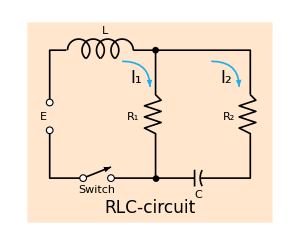

```mathematica
Graphics[{{LightOrange,Rectangle[{1.1,0.3},{3.3,2.1}]},(*{LightGray,Table[{Line[{{1.2,n},{3.3,n}}]},{n,0,2.2,0.1}]},{LightGray,Table[{Line[{{n,0},{n,2.2}}]},{n,1.2,3.3,0.1}]},*){Thickness[0.004],Line[{{1.3,1.11},{1.3,0.7},{1.6,0.7}}]},{Thickness[0.004],Circle[{1.56,1.85},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.69,1.85},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{1.82,1.85},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{1.95,1.85},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.65,0.7},{3.1,0.7},{3.1,1.1},{3,1.15},{3.15,1.2},{3,1.25},{3.15,1.3},{3,1.35},{3.15,1.4},{3.1,1.45}}]},(* 777777 *){Thickness[0.004],Circle[{2.8,0.7},0.15,{π-0.5,π+0.5}]},{Thickness[0.004],Line[{{3.1,1.45},{3.1,1.85},{2.05,1.85}}]},{Thickness[0.004],Line[{{1.45,1.85},{1.3,1.85},{1.3,1.38}}]},{Disk[{2.25,0.7},0.03]},{Disk[{2.25,1.85},0.03]},{Text[Style["R_1",Medium],{2.05,1.25}]},{Text[Style["R_2",Medium],{2.91,1.25}]},{Text[Style["L",Medium],{1.8,2.02}]},{Text[Style["RLC-circuit",17],{2.2,0.43}]},{Text[Style["C",Medium],{2.63,0.55}]},{Text[Style["E",Medium],{1.24,1.25}]},{Text[Style["Switch",Medium],{1.72,0.59}]},{Thickness[0.004],Line[{{2.6,0.775},{2.6,0.625}}]},{Thickness[0.004],Line[{{1.85,0.7},{2.6,0.7}}]},{RGBColor[0.113,0.686,0.925],Thickness[0.004],Arrow[BezierCurve[{{2.75,1.75},{3,1.75},{3,1.52}}]]},{RGBColor[0.113,0.686,0.925],Thickness[0.004],Arrow[BezierCurve[{{1.95,1.75},{2.2,1.75},{2.2,1.52}}]]},{Text[Style["I_1",17],{2.08,1.6}]},{Text[Style["I_2",17],{2.88,1.6}]},{Arrowheads[0.025],Thickness[0.004],Arrow[{{1.6,0.7},{1.85,0.8}}]},{Disk[{1.6,0.7},0.035]},{Disk[{1.85,0.7},0.035]},{White,Disk[{1.6,0.7},0.025]},{White,Disk[{1.85,0.7},0.025]},{Thickness[0.004],Line[{{2.25,1.85},{2.25,1.45},{2.3,1.4},{2.15,1.35},{2.3,1.3},{2.15,1.25},{2.3,1.2},{2.15,1.15},{2.25,1.1},{2.25,0.7}}]},{Disk[{1.3,1.13},0.035]},{Disk[{1.3,1.38},0.035]},{White,Disk[{1.3,1.13},0.025]},{White,Disk[{1.3,1.38},0.025]}},Axes->False,ImageSize->300,Ticks->{Range[0,5,0.1],Range[0,2.2,0.1]}]
```